## HBM

### Setup

```mathematica
solutions=Import[StringJoin[NotebookDirectory[],"training_grid.dat"],"Table"];
Pgrid=Union[solutions[[All,3]]];
```

```mathematica
"log10 P,b,p";
contours=Import[StringJoin[NotebookDirectory[],"detection_contours.dat"],"Table"];
log10Pgrid=Union[contours[[All,1]]];
```

```mathematica
contours2=Table[{{contours[[i,1]],contours[[i,2]]},contours[[i,3]]},{i,1,Length[contours]}];
pcrit=Interpolation[contours2,Method->"Hermite",InterpolationOrder->3];
```

```mathematica
P1856=1.4079393542348777;
p1856=7.78192788242976174;
b1856=7.67245250662721023;
pcrit[Log10[P1856],b1856]
```

```mathematica
DetProb[P_,b_,p_]:=Piecewise[{{1,p≥pcrit[Log10[P],b]},{0,p<pcrit[Log10[P],b]}}];
DetProb[Log10[P1856],b1856,p1856]
```

1

```mathematica
G=6.674*10^(-11);
RSun=6.957*10^8;
ρstar1856=3.2484807427970564*10^8;
Rstar1856=0.0131*RSun;
REarth=6378100;
pobs=7.86;pstd=0.01;
bobs=7.75;bstd=0.01;
prange={0.06998388135624833,13.996776271249676};
brange={0.01,13.066672581313533};
Prange={0.1,10};
Rprange=Rstar1856 prange/REarth;
Rmax=Rprange[[2]];
Rmin=Rprange[[1]];
```

```mathematica
PostProb[P_,b_,Rp_,α_]:=(1/(√(2 π) pstd)Exp[-((Rp REarth)/Rstar1856-pobs)^2/(2 pstd^2)])(1/(√(2 π) bstd)Exp[-(b-bobs)^2/(2 bstd^2)])DetProb[P,b,(Rp REarth)/Rstar1856]((1+(Rp REarth)/Rstar1856)/(((ρstar1856 G P^2)/(3π))^(1/3)))(((-1+α)(Rp)^-α)/((Rmax Rmin)^-α (Rmax^α Rmin-Rmax Rmin^α)))
LogPostProb[P_,b_,Rp_,α_]:=(-((Rp REarth)/Rstar1856-pobs)^2/(2 pstd^2)+1/2 (-Log[2]-Log[π])-Log[pstd])+(-(b-bobs)^2/(2 bstd^2)+1/2 (-Log[2]-Log[π])-Log[bstd])+Log[DetProb[P,b,(Rp REarth)/Rstar1856]]+Log[((1+(Rp REarth)/Rstar1856)/(((ρstar1856 G P^2)/(3π))^(1/3)))]+Log[(((-1+α)(Rp)^-α)/((Rmax Rmin)^-α (Rmax^α Rmin-Rmax Rmin^α)))];
```

### MCMC

```mathematica
jmax=1010000;j=1;Subscript[θ, j]={b1856,Rp1856,0.5};Subscript[logP, j]=LogPostProb[P1856,Subscript[θ, j][[1]],Subscript[θ, j][[2]],Subscript[θ, j][[3]]]
Δθ={bstd,pstd (Rstar1856/REarth),0.25};Label[jloop];θtrial={RandomReal[TruncatedDistribution[{brange[[1]],brange[[2]]},NormalDistribution[Subscript[θ, j][[1]],Δθ[[1]]]]],RandomReal[TruncatedDistribution[{prange[[1]] Rstar1856/REarth,prange[[2]] Rstar1856/REarth},NormalDistribution[Subscript[θ, j][[2]],Δθ[[2]]]]],RandomReal[NormalDistribution[Subscript[θ, j][[3]],Δθ[[3]]]]};logPtrial=LogPostProb[P1856,θtrial[[1]],θtrial[[2]],θtrial[[3]]];If[NumberQ[logPtrial],If[logPtrial>Subscript[logP, j],accept=1,accept=RandomInteger[BernoulliDistribution[Exp[-Abs[logPtrial-Subscript[logP, j]]]]]],accept=0];If[accept==1,j=j+1];If[accept==1,Subscript[θ, j]=θtrial];If[accept==1,Subscript[logP, j]=logPtrial];If[j<jmax,Goto[jloop]];
```

-52.5244

```mathematica
chains=Table[Join[Subscript[θ, j],{Subscript[logP, j]}],{j,1,jmax}];
Dimensions[chains]
"remove burn-in";
meddy=Median[Select[chains[[All,2]],NumberQ[#]&]]
pos=Position[chains,First[Select[chains,#[[2]]≥meddy&]]][[1,1]]
chains=chains[[10001;;1010000]];
Dimensions[chains]
```

```mathematica
chainsthin=Table[chains[[i]],{i,1,Length[chains],10}];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"hbm_posteriors.dat"],chainsthin,"Table"]
```

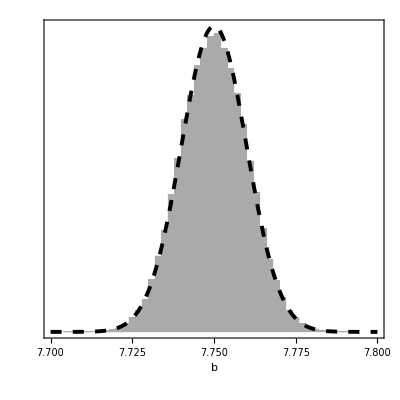

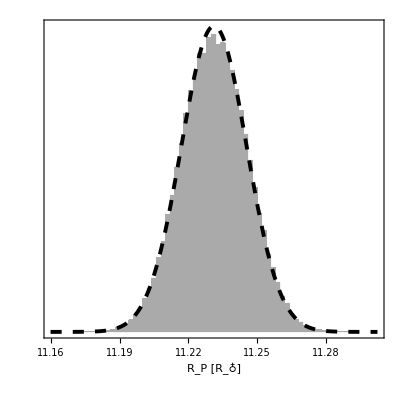

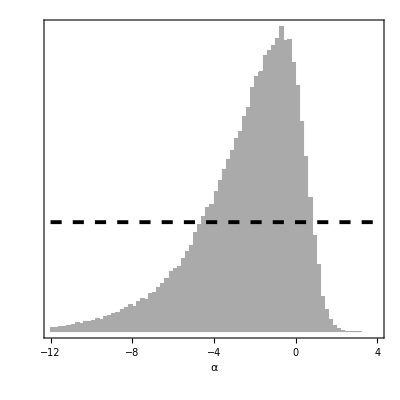

```mathematica
Show[Histogram[chainsthin[[All,1]],50,"PDF",AspectRatio->1,Frame->True,PlotRange->{{bobs-5bstd,bobs+5bstd},{0,All}},FrameLabel->{"b", " "},FrameTicks->{{None,None},{Automatic,None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->18},ImageSize->{400,Automatic},ChartStyle->Directive[Lighter[Gray]]],Plot[PDF[NormalDistribution[bobs,bstd],x],{x,bobs-5bstd,bobs+5bstd},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.007]]]]
Show[Histogram[chainsthin[[All,2]],50,"PDF",AspectRatio->1,Frame->True,PlotRange->{{pobs (Rstar1856/REarth)-5pstd (Rstar1856/REarth),pobs (Rstar1856/REarth)+5pstd (Rstar1856/REarth)},{0,All}},FrameLabel->{"R_P [R_♁]", " "},FrameTicks->{{None,None},{Automatic,None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->18},ImageSize->{400,Automatic},ChartStyle->Directive[Lighter[Gray]]],Plot[PDF[NormalDistribution[pobs (Rstar1856/REarth),pstd (Rstar1856/REarth)],x],{x,pobs (Rstar1856/REarth)-5pstd (Rstar1856/REarth),pobs (Rstar1856/REarth)+5pstd (Rstar1856/REarth)},PlotRange->All,PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.007]]]]
Show[Histogram[Select[chainsthin[[All,3]],-12<#<4&],50,"PDF",AspectRatio->1,Frame->True,PlotRange->{{-12,4},{0,All}},FrameLabel->{"α", " "},FrameTicks->{{None,None},{Automatic,None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->18},ImageSize->{400,Automatic},ChartStyle->Directive[Lighter[Gray]]],Plot[3PDF[UniformDistribution[{-20,20}],x],{x,-12,4},PlotRange->All,PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.007]]]]
```

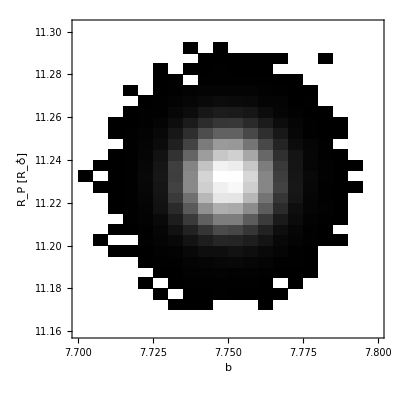

```mathematica
DensityHistogram[chainsthin[[All,{1,2}]],AspectRatio->1,Frame->True,FrameLabel->{"b","R_P [R_♁]"},ImageSize->{400,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->18},PlotRange->{{bobs-5bstd,bobs+5bstd},{pobs (Rstar1856/REarth)-5pstd (Rstar1856/REarth),pobs (Rstar1856/REarth)+5pstd (Rstar1856/REarth)}},ColorFunction->GrayLevel]
```

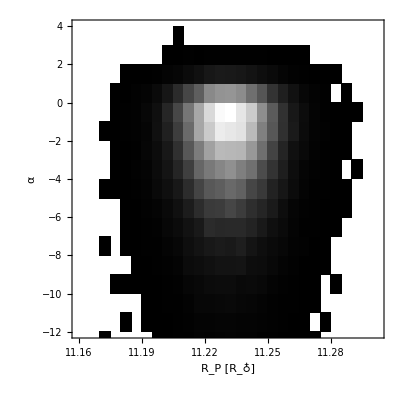

```mathematica
DensityHistogram[chainsthin[[All,{2,3}]],AspectRatio->1,Frame->True,FrameLabel->{"R_P [R_♁]","α"},ImageSize->{400,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->18},PlotRange->{{pobs (Rstar1856/REarth)-5pstd (Rstar1856/REarth),pobs (Rstar1856/REarth)+5pstd (Rstar1856/REarth)},{-12,4}},ColorFunction->GrayLevel]
```

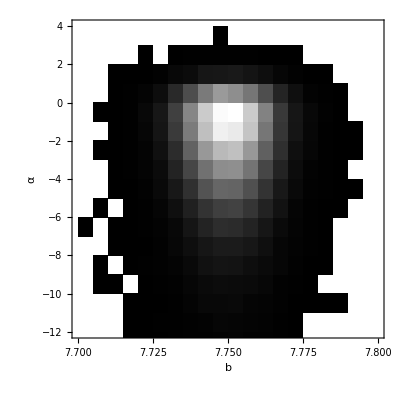

```mathematica
DensityHistogram[chainsthin[[All,{1,3}]],AspectRatio->1,Frame->True,FrameLabel->{"b","α"},ImageSize->{400,Automatic},BaseStyle->{FontFamily->"CMU Serif",FontSize->18},PlotRange->{{bobs-5bstd,bobs+5bstd},{-12,4}},ColorFunction->GrayLevel]
```

```mathematica
100-100N[Length[Select[chainsthin[[All,3]],#>0&]]/Length[chainsthin[[All,3]]]]
```

86.27

```mathematica
{Median[chainsthin[[All,3]]],Median[chainsthin[[All,3]]]-Quantile[chainsthin[[All,3]],0.5-0.5Erf[1/√2]],Quantile[chainsthin[[All,3]],0.5+0.5Erf[1/√2]]-Median[chainsthin[[All,3]]]}
```

{-1.88699,2.94295,1.7681}

## Surprisingness

### Using HBM model

```mathematica
chainsthin=Import[StringJoin[NotebookDirectory[],"hbm_posteriors.dat"],"Table"];
```

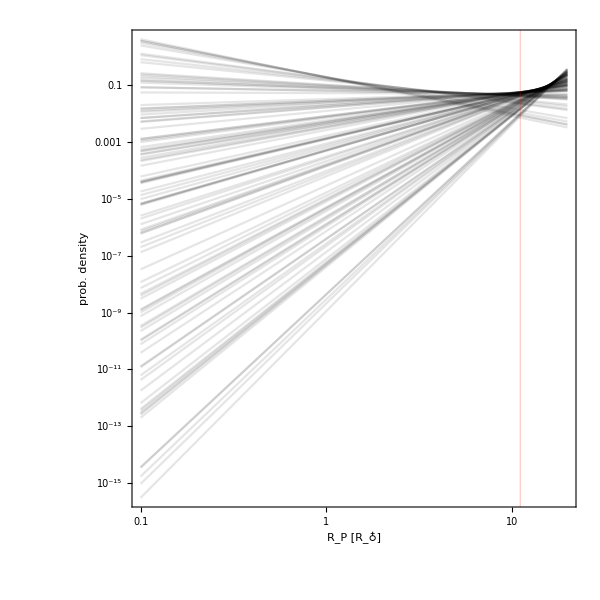

```mathematica
powerlaw[α_,Rp_]:=((-1+α)(Rp)^-α)/((Rmax Rmin)^-α (Rmax^α Rmin-Rmax Rmin^α));
LogLogPlot[Table[powerlaw[chainsthin[[i,3]],R],{i,1,100}],{R,Rprange[[1]],Rprange[[2]]},Frame->True,FrameLabel->{"R_P [R_♁]","prob. density"},PlotStyle->Directive[Black,Opacity[0.1]],ImageSize->{600,Automatic},AspectRatio->1,BaseStyle->{FontFamily->"CMU Serif",FontSize->24},GridLines->{{{Rp1856,Red}},{}}]
```

```mathematica
Rsampler[Rlo_,Rhi_,α_,zz_]:=((Rhi Rlo)^-α (Rhi^α Rlo-Rhi Rlo^α) ((Rhi^α Rlo)/(Rhi^α Rlo-Rhi Rlo^α)-zz))^(1/(1-α))
j=0;jmax=10^5;Label[jloop];Pdraw=Exp[RandomReal[{Log[Prange[[1]]],Log[Prange[[2]]]}]];αdraw=RandomChoice[chainsthin[[All,3]]];Rdraw=Rsampler[Rmin,Rmax,αdraw,RandomReal[]];pdraw=(Rdraw REarth)/Rstar1856;bdraw=RandomReal[{0.01,((ρstar1856 G (86400Pdraw)^2)/(3π))^(1/3)}];detectprob=DetProb[Pdraw,bdraw,pdraw];If[bdraw<1+pdraw&&detectprob==1,j=j+1];If[bdraw<1+pdraw&&detectprob==1,Subscript[λ, j]={Pdraw,bdraw,Rdraw}];If[j<jmax,Goto[jloop]];
```

```mathematica
logPlogblogR=Table[{Log10[Subscript[λ, j][[1]]],Log10[Subscript[λ, j][[2]]],Log10[Subscript[λ, j][[3]]]},{j,1,jmax}];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"hbm_simdetpop.dat"],logPlogblogR,"Table"]
```

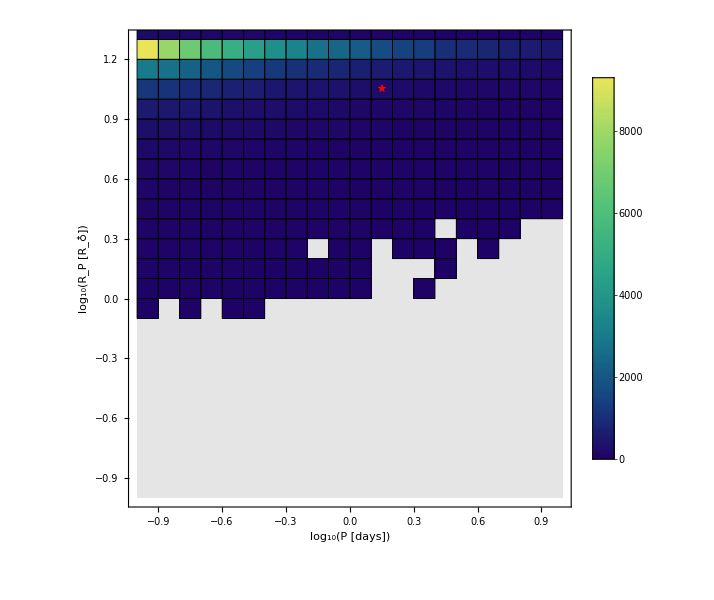

0.88681

```mathematica
Show[Plot[1.03Log10[Rprange[[2]]],{x,Log10[Prange[[1]]],Log10[Prange[[2]]]},Frame->True,Axes->None,PlotRange->{{Log10[Prange[[1]]],Log10[Prange[[2]]]},{Log10[Rprange[[1]]],1.00Log10[Rprange[[2]]]}},FrameLabel->{"log_10(P [days])","log_10(R_P [R_♁])"},ImageSize->{600,Automatic},AspectRatio->1,PlotStyle->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->24},Filling->Bottom,FillingStyle->Directive[Gray,Opacity[0.2]]],DensityHistogram[logPlogblogR[[All,{1,3}]],{0.1},ColorFunction->"BlueGreenYellow",ChartBaseStyle->Directive[FaceForm[Opacity[0.5]],EdgeForm[Directive[Black,Thickness[0.001]]]],ChartLegends->Automatic],ListPlot[{{Log10[P1856],Log10[Rp1856]}},PlotMarkers->"★",PlotStyle->Red]]
N[Length[Select[logPlogblogR[[All,{1,3}]],#[[2]]≥Log10[Rp1856]&]]/Length[logPlogblogR]]
```

```mathematica
powerlawsdraws=Table[Rsampler[Rmin,Rmax,RandomChoice[chainsthin][[3]],RandomReal[]],{i,1,10^5}];
kerny=SmoothKernelDistribution[Log10[powerlawsdraws],0.1,"Biweight"];
```

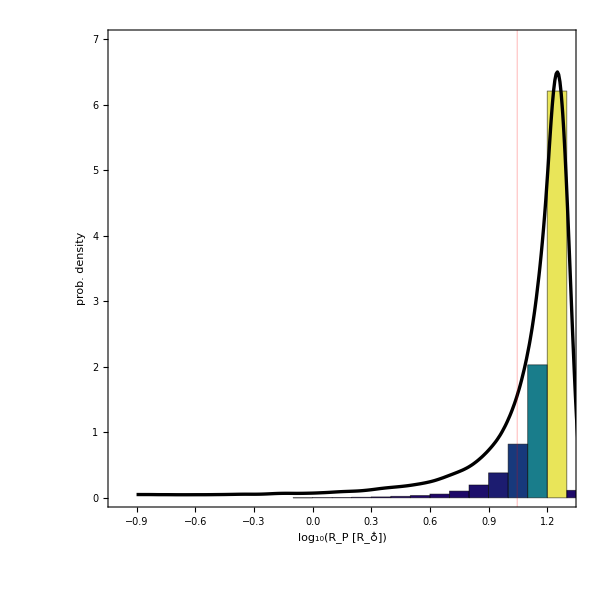

```mathematica
Show[Histogram[logPlogblogR[[All,3]],{0.1},"PDF",Frame->True,FrameLabel->{"log_10(R_P [R_♁])","prob. density"},ImageSize->{600,Automatic},AspectRatio->1,BaseStyle->{FontFamily->"CMU Serif",FontSize->24},PlotRange->{{Log10[Rprange[[1]]],Log10[Rprange[[2]]]},{0,7}},GridLines->{{{Log10[Rp1856],Red}},{}},ColorFunction->Function[{height},ColorData["BlueGreenYellow"][height]],ChartBaseStyle->Directive[FaceForm[Opacity[0.5]],EdgeForm[Directive[Black,Thickness[0.001]]]]],Plot[1.6PDF[kerny,x],{x,-0.9,1.5},PlotRange->All,PlotStyle->Directive[Black,Thickness[0.004]]]]
```

```mathematica
100N[Length[Select[powerlawsdraws,#<2&]]/Length[powerlawsdraws]]
```

5.16

```mathematica
100N[Length[Select[logPlogblogR[[All,3]],#<Log10[2]&]]/Length[logPlogblogR[[All,3]]]]
```

0.187

### Using He+ bottom-heavy distribution

```mathematica
Rfn[Rc_,α1_,α2_,R_,Rlow_,Rhigh_]:=Piecewise[{{Rc^-α2/Rc^-α1 R^-α1,R<Rc},{R^-α2,R>Rc}}]/((Rc^-α2 Rlow^-α1 (Rc^α1 Rlow-Rc Rlow^α1))/(-1+α1)+((Rc Rhigh)^-α2 (-Rc^α2 Rhigh+Rc Rhigh^α2))/(-1+α2))
```

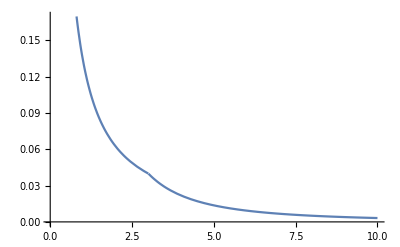

```mathematica
Plot[Rfn[3,1.1,2.1,R,0.01,10],{R,0.01,10}]
```

```mathematica
FullSimplify[Integrate[Rfn[Rc,α1,α2,R,Rlow,Rhigh],{R,Rlow,Rhigh},Assumptions->Rhigh>Rc>Rlow>0]]
```

1

```mathematica
FullSimplify[Integrate[Rfn[Rc,α1,α2,R,Rlow,Rhigh],{R,Rlow,Rx},Assumptions->Rhigh>Rc>Rlow>0&&Rhigh>Rx>Rc>Rlow>0]]
```

(Rc^α2 Rlow^α1 (Rhigh/Rx)^α2 Rx (-1+α1)+Rc Rlow^α1 (-(Rhigh/Rx)^α2 Rx^α2 (-1+α1)+Rhigh^α2 (-1+α2))-Rc^α1 Rhigh^α2 Rlow (-1+α2))/(-Rc^α1 Rhigh^α2 Rlow (-1+α2)+Rlow^α1 (Rc^α2 Rhigh (-1+α1)+Rc Rhigh^α2 (-α1+α2)))

```mathematica
Rcdf[Rc_,α1_,α2_,Rx_,Rlow_,Rhigh_]:=Piecewise[{{(Rhigh^α2 (Rc/Rx)^α1 (Rlow^α1 Rx-Rlow Rx^α1) (-1+α2))/(-Rc^α1 Rhigh^α2 Rlow (-1+α2)+Rlow^α1 (Rc^α2 Rhigh (-1+α1)+Rc Rhigh^α2 (-α1+α2))),Rx<Rc},{(Rc^α2 Rlow^α1 (Rhigh/Rx)^α2 Rx (-1+α1)+Rc Rlow^α1 (-(Rhigh/Rx)^α2 Rx^α2 (-1+α1)+Rhigh^α2 (-1+α2))-Rc^α1 Rhigh^α2 Rlow (-1+α2))/(-Rc^α1 Rhigh^α2 Rlow (-1+α2)+Rlow^α1 (Rc^α2 Rhigh (-1+α1)+Rc Rhigh^α2 (-α1+α2))),Rx>Rc}}];
```

```mathematica
Simplify[Limit[(Rhigh^α2 (Rc/Rx)^α1 (Rlow^α1 Rx-Rlow Rx^α1) (-1+α2))/(-Rc^α1 Rhigh^α2 Rlow (-1+α2)+Rlow^α1 (Rc^α2 Rhigh (-1+α1)+Rc Rhigh^α2 (-α1+α2))),Rx->Rc,Direction->"FromBelow"]==Limit[(Rc^α2 Rlow^α1 (Rhigh/Rx)^α2 Rx (-1+α1)+Rc Rlow^α1 (-(Rhigh/Rx)^α2 Rx^α2 (-1+α1)+Rhigh^α2 (-1+α2))-Rc^α1 Rhigh^α2 Rlow (-1+α2))/(-Rc^α1 Rhigh^α2 Rlow (-1+α2)+Rlow^α1 (Rc^α2 Rhigh (-1+α1)+Rc Rhigh^α2 (-α1+α2))),Rx->Rc,Direction->"FromAbove"]]
```

True

```mathematica
Limit[(Rhigh^α2 (Rc/Rx)^α1 (Rlow^α1 Rx-Rlow Rx^α1) (-1+α2))/(-Rc^α1 Rhigh^α2 Rlow (-1+α2)+Rlow^α1 (Rc^α2 Rhigh (-1+α1)+Rc Rhigh^α2 (-α1+α2))),Rx->Rc,Direction->"FromBelow"]
```

(Rhigh^α2 (-Rc^α1 Rlow+Rc Rlow^α1) (-1+α2))/(-Rc^α1 Rhigh^α2 Rlow (-1+α2)+Rlow^α1 (Rc^α2 Rhigh (-1+α1)+Rc Rhigh^α2 (-α1+α2)))

```mathematica
zcrit[Rc_,α1_,α2_,Rlow_,Rhigh_]:=(Rhigh^α2 (-Rc^α1 Rlow+Rc Rlow^α1) (-1+α2))/(-Rc^α1 Rhigh^α2 Rlow (-1+α2)+Rlow^α1 (Rc^α2 Rhigh (-1+α1)+Rc Rhigh^α2 (-α1+α2)));
```

```mathematica
Rsamplelow[Rc_,α1_,α2_,Rlow_,Rhigh_,z_]:=ⅇ^((-ⅈ π-Log[-z+(Rc^α1 Rhigh^α2 Rlow)/(Rc^α1 Rhigh^α2 Rlow-Rc^α2 Rhigh Rlow^α1+Rc^α2 Rhigh Rlow^α1 α1-Rc Rhigh^α2 Rlow^α1 α1-Rc^α1 Rhigh^α2 Rlow α2+Rc Rhigh^α2 Rlow^α1 α2)-(Rc^α1 Rhigh^α2 Rlow α2)/(Rc^α1 Rhigh^α2 Rlow-Rc^α2 Rhigh Rlow^α1+Rc^α2 Rhigh Rlow^α1 α1-Rc Rhigh^α2 Rlow^α1 α1-Rc^α1 Rhigh^α2 Rlow α2+Rc Rhigh^α2 Rlow^α1 α2)]+Log[-(Rc^α1 Rhigh^α2 Rlow^α1)/(Rc^α1 Rhigh^α2 Rlow-Rc^α2 Rhigh Rlow^α1+Rc^α2 Rhigh Rlow^α1 α1-Rc Rhigh^α2 Rlow^α1 α1-Rc^α1 Rhigh^α2 Rlow α2+Rc Rhigh^α2 Rlow^α1 α2)+(Rc^α1 Rhigh^α2 Rlow^α1 α2)/(Rc^α1 Rhigh^α2 Rlow-Rc^α2 Rhigh Rlow^α1+Rc^α2 Rhigh Rlow^α1 α1-Rc Rhigh^α2 Rlow^α1 α1-Rc^α1 Rhigh^α2 Rlow α2+Rc Rhigh^α2 Rlow^α1 α2)])/(-1+α1));
Rsamplehigh[Rc_,α1_,α2_,Rlow_,Rhigh_,z_]:=((Rc^α2 Rhigh^α2 Rlow^α1 (-1+α1))/(-Rc^α1 Rhigh^α2 Rlow+Rc^α1 Rhigh^α2 Rlow z-Rc^α2 Rhigh Rlow^α1 z+Rc Rhigh^α2 Rlow^α1 α1+Rc^α2 Rhigh Rlow^α1 z α1-Rc Rhigh^α2 Rlow^α1 z α1+Rc^α1 Rhigh^α2 Rlow α2-Rc Rhigh^α2 Rlow^α1 α2-Rc^α1 Rhigh^α2 Rlow z α2+Rc Rhigh^α2 Rlow^α1 z α2))^(1/(-1+α2));
Rmegasample[Rc_,α1_,α2_,Rlow_,Rhigh_,z_]:=Piecewise[{{Rsamplelow[Rc,α1,α2,Rlow,Rhigh,z],z<zcrit[Rc,α1,α2,Rlow,Rhigh]},{Rsamplehigh[Rc,α1,α2,Rlow,Rhigh,z],z>zcrit[Rc,α1,α2,Rlow,Rhigh]}}];
```

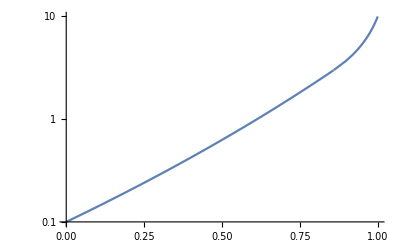

```mathematica
LogPlot[Rmegasample[3,1.1,2.1,0.1,10,z],{z,0,1}]
```

```mathematica
"define a mixture distribution";
xmin=-∞;xmax=∞;
αdist=MixtureDistribution[{Limit[PDF[TruncatedDistribution[{xmin,μ},NormalDistribution[μ,σneg]],x],x->μ,Direction->"FromBelow"],Limit[PDF[TruncatedDistribution[{μ,xmax},NormalDistribution[μ,σpos]],x],x->μ,Direction->"FromAbove"]},{TruncatedDistribution[{μ,xmax},NormalDistribution[μ,σpos]],TruncatedDistribution[{xmin,μ},NormalDistribution[μ,σneg]]}];
α1dist=αdist/.μ->-1.08/.σneg->0.20/.σpos->0.31;
α2dist=αdist/.μ->-5.30/.σneg->0.40/.σpos->0.53;
```

```mathematica
α1draws=-RandomVariate[α1dist,10^6];
α2draws=-RandomVariate[α2dist,10^6];
```

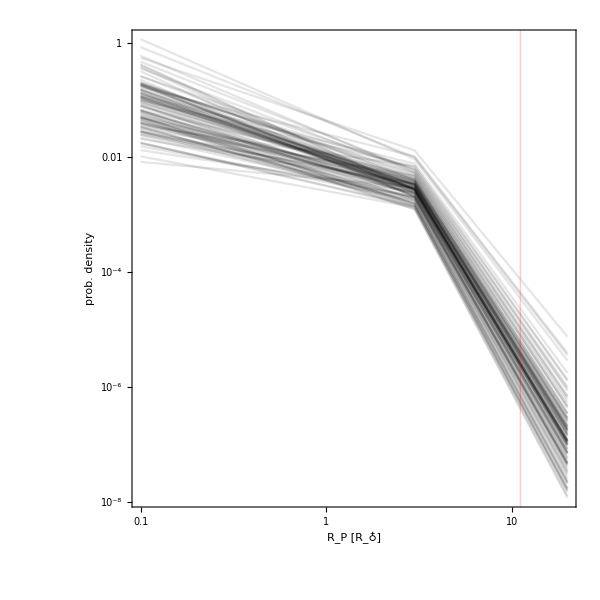

```mathematica
LogLogPlot[Table[Rfn[3,α1draws[[i]],α2draws[[i]],R]/.Rlow->Rprange[[1]]/.Rhigh->Rprange[[2]],{i,1,100}],{R,Rprange[[1]],Rprange[[2]]},Frame->True,FrameLabel->{"R_P [R_♁]","prob. density"},PlotStyle->Directive[Black,Opacity[0.1]],ImageSize->{600,Automatic},AspectRatio->1,BaseStyle->{FontFamily->"CMU Serif",FontSize->24},GridLines->{{{Rp1856,Red}},{}}]
```

```mathematica
Median[Table[Integrate[Rfn[3,α1draws[[i]],α2draws[[i]],R]/.Rlow->Rprange[[1]]/.Rhigh->Rprange[[2]],{R,Rprange[[1]],2}],{i,1,1000}]]
```

0.0300033

```mathematica
j=0;tstart=AbsoluteTime[];jmax=10^5;Label[jloop];Pdraw=Exp[RandomReal[{Log[Prange[[1]]],Log[Prange[[2]]]}]];α1draw=RandomChoice[α1draws];α2draw=RandomChoice[α2draws];Rdraw=Re[Rmegasample[3,α1draw,α2draw,Rmin,Rmax,RandomReal[]]];pdraw=(Rdraw REarth)/Rstar1856;bdraw=RandomReal[{0.01,((ρstar1856 G (86400Pdraw)^2)/(3π))^(1/3)}];detectprob=DetProb[Pdraw,bdraw,pdraw];If[bdraw<1+pdraw&&detectprob==1,j=j+1];If[bdraw<1+pdraw&&detectprob==1,Subscript[λ, j]={Pdraw,bdraw,Rdraw}];If[j<jmax,Goto[jloop]];tend=AbsoluteTime[];
```

```mathematica
logPlogblogR=Table[{Log10[Subscript[λ, j][[1]]],Log10[Subscript[λ, j][[2]]],Log10[Subscript[λ, j][[3]]]},{j,1,jmax}];
```

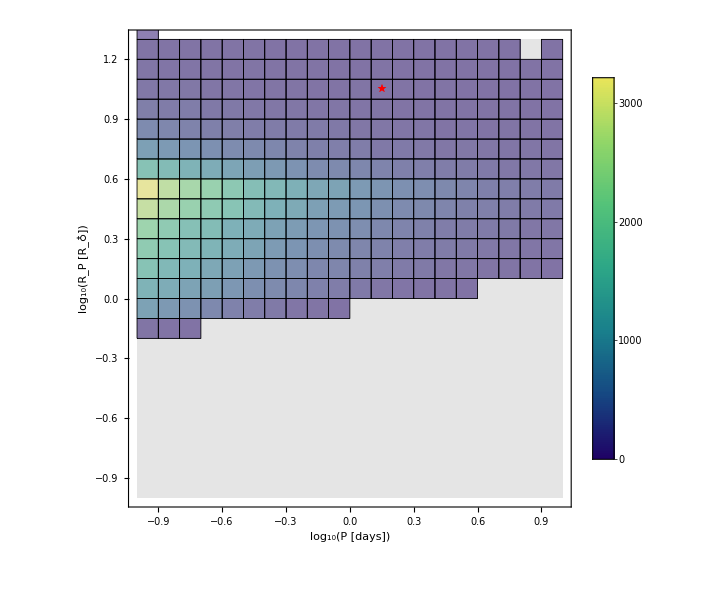

0.00752

```mathematica
Show[Plot[1.03Log10[Rprange[[2]]],{x,Log10[Prange[[1]]],Log10[Prange[[2]]]},Frame->True,Axes->None,PlotRange->{{Log10[Prange[[1]]],Log10[Prange[[2]]]},{Log10[Rprange[[1]]],1.0Log10[Rprange[[2]]]}},FrameLabel->{"log_10(P [days])","log_10(R_P [R_♁])"},ImageSize->{600,Automatic},AspectRatio->1,PlotStyle->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->24},Filling->Bottom,FillingStyle->Directive[Gray,Opacity[0.2]]],DensityHistogram[logPlogblogR[[All,{1,3}]],{0.1},ColorFunction->"BlueGreenYellow",ChartBaseStyle->Directive[FaceForm[Opacity[0.5]],EdgeForm[Directive[Black,Thickness[0.001]]]],ChartLegends->Automatic],ListPlot[{{Log10[P1856],Log10[Rp1856]}},PlotMarkers->"★",PlotStyle->Red]]
N[Length[Select[logPlogblogR[[All,{1,3}]],#[[2]]≥Log10[Rp1856]&]]/Length[logPlogblogR]]
```

```mathematica
Ralldraws=Select[Table[Re[Rmegasample[3,α1draws[[i]],α2draws[[i]],Rmin,Rmax,RandomReal[]]],{i,1,10^5}],Rmin<#<Rmax&];
kerny=SmoothKernelDistribution[Ralldraws,0.05,"Biweight"];
```

```mathematica
N[Length[Select[Ralldraws,#<2&]]/Length[Ralldraws]]
```

0.828959

```mathematica
logkerny=SmoothKernelDistribution[Log10[Ralldraws],0.14,"Gaussian"];
```

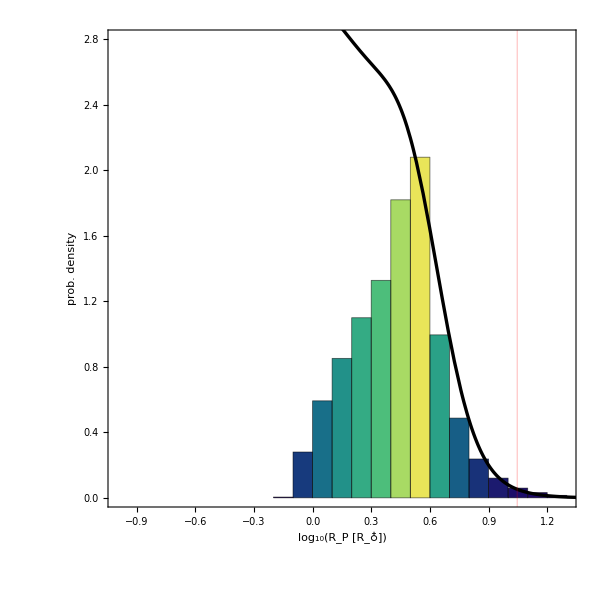

```mathematica
Show[Histogram[logPlogblogR[[All,3]],{0.1},"PDF",Frame->True,FrameLabel->{"log_10(R_P [R_♁])","prob. density"},ImageSize->{600,Automatic},AspectRatio->1,BaseStyle->{FontFamily->"CMU Serif",FontSize->24},GridLines->{{{Log10[Rp1856],Red}},{}},PlotRange->{{Log10[Rprange[[1]]],Log10[Rprange[[2]]]},{0,2.8}},ColorFunction->Function[{height},ColorData["BlueGreenYellow"][height]],ChartBaseStyle->Directive[FaceForm[Opacity[0.5]],EdgeForm[Directive[Black,Thickness[0.001]]]]],Plot[5.4PDF[logkerny,x],{x,-0.08,1.5},PlotStyle->Directive[Black,Thickness[0.004]]]]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"he_simdetpop.dat"],logPlogblogR,"Table"]
```

```mathematica
100N[Length[Select[logPlogblogR[[All,3]],#<Log10[2]&]]/Length[logPlogblogR[[All,3]]]]
```

28.378

### Usint Fulton+ top-heavy distribution

```mathematica
fultonRs=Flatten[Import[StringJoin[NotebookDirectory[],"fulton_Rsims.dat"],"Table"]];
```

```mathematica
100N[Length[Select[fultonRs,#<2&]]/Length[fultonRs]]
```

0.0164

```mathematica
j=0;tstart=AbsoluteTime[];jmax=10^5;Label[jloop];Pdraw=Exp[RandomReal[{Log[Prange[[1]]],Log[Prange[[2]]]}]];Rdraw=RandomChoice[fultonRs];pdraw=(Rdraw REarth)/Rstar1856;bdraw=RandomReal[{0.01,((ρstar1856 G (86400Pdraw)^2)/(3π))^(1/3)}];detectprob=DetProb[Pdraw,bdraw,pdraw];If[bdraw<1+pdraw&&detectprob==1,j=j+1];If[bdraw<1+pdraw&&detectprob==1,Subscript[λ, j]={Pdraw,bdraw,Rdraw}];If[j<jmax,Goto[jloop]];tend=AbsoluteTime[];
```

```mathematica
logPlogblogR=Table[{Log10[Subscript[λ, j][[1]]],Log10[Subscript[λ, j][[2]]],Log10[Subscript[λ, j][[3]]]},{j,1,jmax}];
```

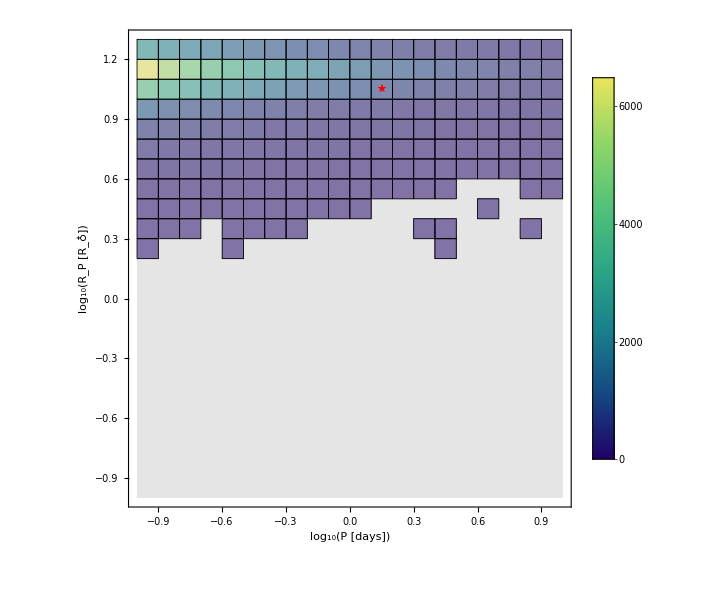

0.78399

```mathematica
Show[Plot[1.03Log10[Rprange[[2]]],{x,Log10[Prange[[1]]],Log10[Prange[[2]]]},Frame->True,Axes->None,PlotRange->{{Log10[Prange[[1]]],Log10[Prange[[2]]]},{Log10[Rprange[[1]]],1.00Log10[Rprange[[2]]]}},FrameLabel->{"log_10(P [days])","log_10(R_P [R_♁])"},ImageSize->{600,Automatic},AspectRatio->1,PlotStyle->None,BaseStyle->{FontFamily->"CMU Serif",FontSize->24},Filling->Bottom,FillingStyle->Directive[Gray,Opacity[0.2]]],DensityHistogram[logPlogblogR[[All,{1,3}]],{0.1},ColorFunction->"BlueGreenYellow",ChartBaseStyle->Directive[FaceForm[Opacity[0.5]],EdgeForm[Directive[Black,Thickness[0.001]]]],ChartLegends->Automatic],ListPlot[{{Log10[P1856],Log10[Rp1856]}},PlotMarkers->"★",PlotStyle->Red]]
N[Length[Select[logPlogblogR[[All,{1,3}]],#[[2]]≥Log10[Rp1856]&]]/Length[logPlogblogR]]
```

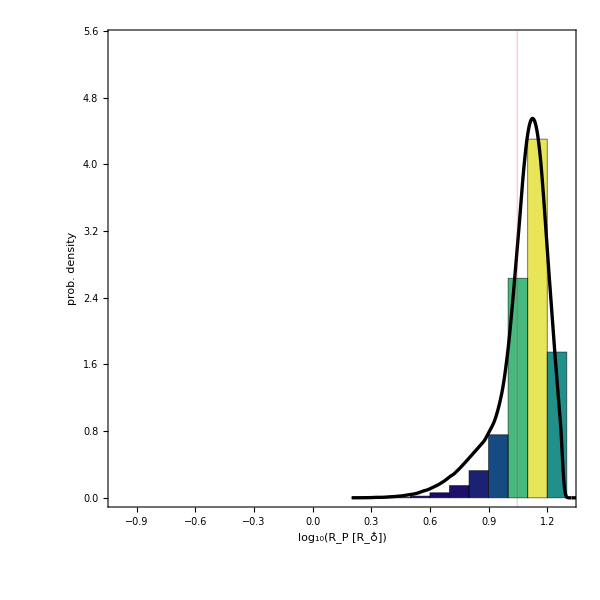

```mathematica
kerny=SmoothKernelDistribution[Log10[fultonRs],"Silverman","Gaussian"];
Show[Histogram[logPlogblogR[[All,3]],{0.1},"PDF",Frame->True,FrameLabel->{"log_10(R_P [R_♁])","prob. density"},ImageSize->{600,Automatic},AspectRatio->1,BaseStyle->{FontFamily->"CMU Serif",FontSize->24},GridLines->{{{Log10[Rp1856],Red}},{}},PlotRange->{{Log10[Rprange[[1]]],Log10[Rprange[[2]]]},{0,5.5}},ColorFunction->Function[{height},ColorData["BlueGreenYellow"][height]],ChartBaseStyle->Directive[FaceForm[Opacity[0.5]],EdgeForm[Directive[Black,Thickness[0.001]]]]],Plot[1.1PDF[kerny,x],{x,0.2,1.7},PlotStyle->Directive[Black,Thickness[0.004]]]]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"fulton_simdetpop.dat"],logPlogblogR,"Table"]
```

/Users/dkipping/Storage1/Work/Documents/Transit_Work/PAPERS/TESS/WD1856/fulton_forward.dat

```mathematica
100N[Length[Select[logPlogblogR[[All,3]],#<Log10[2]&]]/Length[logPlogblogR[[All,3]]]]
```

0.004

```mathematica
100N[Length[Select[fultonRs,#<2&]]/Length[fultonRs]]
```

0.0164